### Scale Factor a(t) in Λ_sCDM (The cosmic time is rescaled as t->t/t_s):

```mathematica
ω[om_,ol_]:=ol/om;
(*Defining some cuttoff functions*)
cutoff[x_,τ_]:=If[x≥τ,1,None];
cutoff1[x_,τ_]:=If[x≤τ,1,None];
(*scale factor*)
a[t_,om_,H0ts_]:=Piecewise[{{(om/(1-om))^(1/3)Sin[3/2 H0ts √(1-om)t]^(2/3),t≤1},{(om/(1-om))^(1/3)Sinh[3/2 H0ts √(1-om)(t-1)+ArcSinh[Sin[3/2 H0ts √(1-om)]]]^(2/3),t≥1}}];
(*Friedmann equation in LsCDM*)
Hubble[a_,om_,ol_,H0_,as_]:=Sqrt[om H0^2 (a^(-3)+(2HeavisideTheta[1/as-1/a]-1)ω[om,ol])];
(*Calculating \ddot{a}/a*)
```

```mathematica
FullSimplify[α Hubble[α,om,ol,H0,as]D[Hubble[α,om,ol,H0,as],{α,1}]+Hubble[α,om,ol,H0,as]^2]
```

1/2 H0^2 om α (-3/α^4+(2 ol DiracDelta[1/as-1/α])/(om α^2))+H0^2 (-ol+om/α^3+2 ol HeavisideTheta[1/as-1/α])

```mathematica
FullSimplify[D[a[t,om,H0ts],{t,2}]/a[t,om,H0ts]]
```

Piecewise[{{H0ts^2 (-1+om) (1+1/(1-Cos[3 H0ts √(1-om) t])), t<1}, {1/2 H0ts^2 (-1+om) (-2+Csch[3/2 H0ts √(1-om) (-1+t)+ArcSinh[Sin[3/2 H0ts √(1-om)]]]^2), t>1}, {Indeterminate, True}}]

```mathematica
Force[α_,om_,ol_,H0ts_,as_]:=1/2 H0ts^2 om α (-3/α^4+(2 ol DiracDelta[1/as-1/α])/(om α^2))+H0ts^2 (-ol+om/α^3+2 ol HeavisideTheta[1/as-1/α]);
(*After we solve the geodesic equation of the free particle \ddot{r}=\ddot{a}/a r, before and after Subscript[t, s] and we obtain (rminus represent the rescaled radius r/r0 before t_s):*)
```

```mathematica
rminus[τ_,om_,H0ts_,A_,B_]:=A (-1+Cos[3/2 H0ts Sqrt[1-om] τ]^2)^(1/4)*LegendreP[1/6,1/6,Cos[3/2 H0ts Sqrt[1-om] τ]]+B (-1+Cos[3/2 H0ts Sqrt[1-om] τ]^2)^(1/4)*LegendreQ[1/6,1/6,Cos[3/2 H0ts Sqrt[1-om] τ]];
rplus[τ_,om_,H0ts_,H_,F_]:=((Sech[3/2 H0ts Sqrt[1-om] (τ-1)+ArcSinh[Sin[3/2 H0ts Sqrt[1-om]]]]^2)^(1/6) (-3 H Hypergeometric2F1[-(1/6),1/3,5/6,Tanh[3/2 H0ts Sqrt[1-om] (τ-1)+ArcSinh[Sin[3/2 H0ts Sqrt[1-om]]]]^2]+F Tanh[3/2 H0ts Sqrt[1-om] (τ-1)+ArcSinh[Sin[3/2 H0ts Sqrt[1-om]]]]^(1/3)) Tanh[3/2 H0ts Sqrt[1-om] (τ-1)+ArcSinh[Sin[3/2 H0ts Sqrt[1-om]]]]^(1/3))/(Sqrt[-Sech[3/2 H0ts Sqrt[1-om] (τ-1)+ArcSinh[Sin[3/2 H0ts Sqrt[1-om]]]]^2]);
(*Derivative of r(t) in each region*)
r1minus[τ_,om_,H0ts_,A1_,B1_]:=(H0ts Sqrt[1-om] (2 A1 Cos[3/2 H0ts Sqrt[1-om] τ] LegendreP[1/6,1/6,Cos[3/2 H0ts Sqrt[1-om] τ]]-3 A1 LegendreP[7/6,1/6,Cos[3/2 H0ts Sqrt[1-om] τ]]+2 B1 Cos[3/2 H0ts Sqrt[1-om] τ] LegendreQ[1/6,1/6,Cos[3/2 H0ts Sqrt[1-om] τ]]-3 B1 LegendreQ[7/6,1/6,Cos[3/2 H0ts Sqrt[1-om] τ]]) Sin[3/2 H0ts Sqrt[1-om] τ])/(2^(1/4) (-1+Cos[3 H0ts Sqrt[1-om] τ])^(3/4));
r1plus[τ_,om_,H0ts_,H1_,F1_]:=(H0ts Sqrt[1-om] (Sech[3/2 H0ts Sqrt[1-om] (-1+τ)+ArcSinh[Sin[3/2 H0ts Sqrt[1-om]]]]^2)^(1/6) (3 H1 (1/(1+Cosh[3 H0ts Sqrt[1-om] (-1+τ)+2 ArcSinh[Sin[3/2 H0ts Sqrt[1-om]]]]))^(2/3)-3 2^(1/3) H1 Hypergeometric2F1[-(1/6),1/3,5/6,Tanh[3/2 H0ts Sqrt[1-om] (-1+τ)+ArcSinh[Sin[3/2 H0ts Sqrt[1-om]]]]^2]+F1 (Sech[3/2 H0ts Sqrt[1-om] (-1+τ)+ArcSinh[Sin[3/2 H0ts Sqrt[1-om]]]] (2 Cosh[3/2 H0ts Sqrt[1-om] (-1+τ)] Sin[3/2 H0ts Sqrt[1-om]]+Sqrt[6-2 Cos[3 H0ts Sqrt[1-om]]] Sinh[3/2 H0ts Sqrt[1-om] (-1+τ)]))^(1/3)))/(2^(1/3) Sqrt[-Sech[3/2 H0ts Sqrt[1-om] (-1+τ)+ArcSinh[Sin[3/2 H0ts Sqrt[1-om]]]]^2] Tanh[3/2 H0ts Sqrt[1-om] (-1+τ)+ArcSinh[Sin[3/2 H0ts Sqrt[1-om]]]]^(2/3));
```

### Boundary conditions [r(t_s) continuous and \dot{r}plus(t_s)-\dot{r}minus(t_s)=δH r(t_s) are imposed and the A1,B1,H,F constants are determined:

```mathematica
Hubbleminus[a_,om_,ol_,H0_]:=Sqrt[om H0^2 (a^(-3)-ω[om,ol])];
Hubbleplus[a_,om_,ol_,H0_]:=Sqrt[om H0^2 (a^(-3)+ω[om,ol])];

deltaH[as_,om_,ol_,H0_]:=Sqrt[om H0^2 (as^(-3)+ω[om,ol])]-Sqrt[om H0^2 (as^(-3)-ω[om,ol])];
```

```mathematica
Simplify[Solve[rplus[1,om,H0ts,H1,F1]==rminus[1,om,H0ts,A1,B1]&&( r1plus[1,om,H0ts,H1,F1]-r1minus[1,om,H0ts,A1,B1])==rminus[1,om,H0ts,A1,B1]H0ts(√(om ((om/(1-om))^(1/3) Sin[3/2 H0ts √(1-om) ]^(2/3))^-3+1-om)-√(om ((om/(1-om))^(1/3) Sin[3/2 H0ts √(1-om) ]^(2/3))^-3-1+om)),{H1,F1}]]
```

{{H1→(2^(1/4) (1/(-3+Cos[3 H0ts √(1-om)]))^(3/2) Sin[3/2 H0ts √(1-om)]^2 (3 A1 √(2-2 om) √(3-Cos[3 H0ts √(1-om)]) LegendreP[7/6,1/6,Cos[3/2 H0ts √(1-om)]]+3 B1 √(2-2 om) √(3-Cos[3 H0ts √(1-om)]) LegendreQ[7/6,1/6,Cos[3/2 H0ts √(1-om)]]-2 A1 LegendreP[1/6,1/6,Cos[3/2 H0ts √(1-om)]] (3 √(1-om)+√(2-2 om) Cos[3/2 H0ts √(1-om)] √(3-Cos[3 H0ts √(1-om)])-√(1-om) Cos[3 H0ts √(1-om)]+√(6-2 Cos[3 H0ts √(1-om)]) √(-(-1+om) Cot[3/2 H0ts √(1-om)]^2) Sin[3/2 H0ts √(1-om)]-√(6-2 Cos[3 H0ts √(1-om)]) √(-(-1+om) (1+Csc[3/2 H0ts √(1-om)]^2)) Sin[3/2 H0ts √(1-om)])-2 B1 LegendreQ[1/6,1/6,Cos[3/2 H0ts √(1-om)]] (3 √(1-om)+√(2-2 om) Cos[3/2 H0ts √(1-om)] √(3-Cos[3 H0ts √(1-om)])-√(1-om) Cos[3 H0ts √(1-om)]+√(6-2 Cos[3 H0ts √(1-om)]) √(-(-1+om) Cot[3/2 H0ts √(1-om)]^2) Sin[3/2 H0ts √(1-om)]-√(6-2 Cos[3 H0ts √(1-om)]) √(-(-1+om) (1+Csc[3/2 H0ts √(1-om)]^2)) Sin[3/2 H0ts √(1-om)])))/(3 √(1-om) (1/(3-Cos[3 H0ts √(1-om)]))^(5/6) (-1+Cos[3 H0ts √(1-om)])^(3/4) (Sin[3/2 H0ts √(1-om)]/(√(3-Cos[3 H0ts √(1-om)])))^(1/3)),F1→-((2^(1/12) (1/(-3+Cos[3 H0ts √(1-om)]))^(3/2) Sin[3/2 H0ts √(1-om)]^2 (2^(2/3) √(1-om) (1/(3-Cos[3 H0ts √(1-om)]))^(2/3) (-3+Cos[3 H0ts √(1-om)]) (A1 LegendreP[1/6,1/6,Cos[3/2 H0ts √(1-om)]]+B1 LegendreQ[1/6,1/6,Cos[3/2 H0ts √(1-om)]])+Hypergeometric2F1[-1/6,1/3,5/6,-(2 Sin[3/2 H0ts √(1-om)]^2)/(-3+Cos[3 H0ts √(1-om)])] (-3 A1 √(2-2 om) √(3-Cos[3 H0ts √(1-om)]) LegendreP[7/6,1/6,Cos[3/2 H0ts √(1-om)]]-3 B1 √(2-2 om) √(3-Cos[3 H0ts √(1-om)]) LegendreQ[7/6,1/6,Cos[3/2 H0ts √(1-om)]]+2 A1 LegendreP[1/6,1/6,Cos[3/2 H0ts √(1-om)]] (3 √(1-om)+√(2-2 om) Cos[3/2 H0ts √(1-om)] √(3-Cos[3 H0ts √(1-om)])-√(1-om) Cos[3 H0ts √(1-om)]+√(6-2 Cos[3 H0ts √(1-om)]) √(-(-1+om) Cot[3/2 H0ts √(1-om)]^2) Sin[3/2 H0ts √(1-om)]-√(6-2 Cos[3 H0ts √(1-om)]) √(-(-1+om) (1+Csc[3/2 H0ts √(1-om)]^2)) Sin[3/2 H0ts √(1-om)])+2 B1 LegendreQ[1/6,1/6,Cos[3/2 H0ts √(1-om)]] (3 √(1-om)+√(2-2 om) Cos[3/2 H0ts √(1-om)] √(3-Cos[3 H0ts √(1-om)])-√(1-om) Cos[3 H0ts √(1-om)]+√(6-2 Cos[3 H0ts √(1-om)]) √(-(-1+om) Cot[3/2 H0ts √(1-om)]^2) Sin[3/2 H0ts √(1-om)]-√(6-2 Cos[3 H0ts √(1-om)]) √(-(-1+om) (1+Csc[3/2 H0ts √(1-om)]^2)) Sin[3/2 H0ts √(1-om)]))))/(√(1-om) (1/(3-Cos[3 H0ts √(1-om)]))^(5/6) (-1+Cos[3 H0ts √(1-om)])^(3/4) (Sin[3/2 H0ts √(1-om)]/(√(3-Cos[3 H0ts √(1-om)])))^(2/3)))}}

```mathematica
(*H,F defined in terms of A1,B1 by imposing the boundary conditions*)
```

```mathematica
H[om_,H0ts_,A1_,B1_]:=(2^(1/4) (1/(-3+Cos[3 H0ts √(1-om)]))^(3/2) Sin[3/2 H0ts √(1-om)]^2 (3 A1 √(2-2 om) √(3-Cos[3 H0ts √(1-om)]) LegendreP[7/6,1/6,Cos[3/2 H0ts √(1-om)]]+3 B1 √(2-2 om) √(3-Cos[3 H0ts √(1-om)]) LegendreQ[7/6,1/6,Cos[3/2 H0ts √(1-om)]]-2 A1 LegendreP[1/6,1/6,Cos[3/2 H0ts √(1-om)]] (3 √(1-om)+√(2-2 om) Cos[3/2 H0ts √(1-om)] √(3-Cos[3 H0ts √(1-om)])-√(1-om) Cos[3 H0ts √(1-om)]+√(6-2 Cos[3 H0ts √(1-om)]) √(-(-1+om) Cot[3/2 H0ts √(1-om)]^2) Sin[3/2 H0ts √(1-om)]-√(6-2 Cos[3 H0ts √(1-om)]) √(-(-1+om) (1+Csc[3/2 H0ts √(1-om)]^2)) Sin[3/2 H0ts √(1-om)])-2 B1 LegendreQ[1/6,1/6,Cos[3/2 H0ts √(1-om)]] (3 √(1-om)+√(2-2 om) Cos[3/2 H0ts √(1-om)] √(3-Cos[3 H0ts √(1-om)])-√(1-om) Cos[3 H0ts √(1-om)]+√(6-2 Cos[3 H0ts √(1-om)]) √(-(-1+om) Cot[3/2 H0ts √(1-om)]^2) Sin[3/2 H0ts √(1-om)]-√(6-2 Cos[3 H0ts √(1-om)]) √(-(-1+om) (1+Csc[3/2 H0ts √(1-om)]^2)) Sin[3/2 H0ts √(1-om)])))/(3 √(1-om) (1/(3-Cos[3 H0ts √(1-om)]))^(5/6) (-1+Cos[3 H0ts √(1-om)])^(3/4) (Sin[3/2 H0ts √(1-om)]/(√(3-Cos[3 H0ts √(1-om)])))^(1/3));
F[om_,H0ts_,A1_,B1_]:=-((2^(1/12) (1/(-3+Cos[3 H0ts √(1-om)]))^(3/2) Sin[3/2 H0ts √(1-om)]^2 (2^(2/3) √(1-om) (1/(3-Cos[3 H0ts √(1-om)]))^(2/3) (-3+Cos[3 H0ts √(1-om)]) (A1 LegendreP[1/6,1/6,Cos[3/2 H0ts √(1-om)]]+B1 LegendreQ[1/6,1/6,Cos[3/2 H0ts √(1-om)]])+Hypergeometric2F1[-1/6,1/3,5/6,-(2 Sin[3/2 H0ts √(1-om)]^2)/(-3+Cos[3 H0ts √(1-om)])] (-3 A1 √(2-2 om) √(3-Cos[3 H0ts √(1-om)]) LegendreP[7/6,1/6,Cos[3/2 H0ts √(1-om)]]-3 B1 √(2-2 om) √(3-Cos[3 H0ts √(1-om)]) LegendreQ[7/6,1/6,Cos[3/2 H0ts √(1-om)]]+2 A1 LegendreP[1/6,1/6,Cos[3/2 H0ts √(1-om)]] (3 √(1-om)+√(2-2 om) Cos[3/2 H0ts √(1-om)] √(3-Cos[3 H0ts √(1-om)])-√(1-om) Cos[3 H0ts √(1-om)]+√(6-2 Cos[3 H0ts √(1-om)]) √(-(-1+om) Cot[3/2 H0ts √(1-om)]^2) Sin[3/2 H0ts √(1-om)]-√(6-2 Cos[3 H0ts √(1-om)]) √(-(-1+om) (1+Csc[3/2 H0ts √(1-om)]^2)) Sin[3/2 H0ts √(1-om)])+2 B1 LegendreQ[1/6,1/6,Cos[3/2 H0ts √(1-om)]] (3 √(1-om)+√(2-2 om) Cos[3/2 H0ts √(1-om)] √(3-Cos[3 H0ts √(1-om)])-√(1-om) Cos[3 H0ts √(1-om)]+√(6-2 Cos[3 H0ts √(1-om)]) √(-(-1+om) Cot[3/2 H0ts √(1-om)]^2) Sin[3/2 H0ts √(1-om)]-√(6-2 Cos[3 H0ts √(1-om)]) √(-(-1+om) (1+Csc[3/2 H0ts √(1-om)]^2)) Sin[3/2 H0ts √(1-om)]))))/(√(1-om) (1/(3-Cos[3 H0ts √(1-om)]))^(5/6) (-1+Cos[3 H0ts √(1-om)])^(3/4) (Sin[3/2 H0ts √(1-om)]/(√(3-Cos[3 H0ts √(1-om)])))^(2/3)));
```

### Initial Conditions are imposed and A1,B1 constants are determined

```mathematica
Solve[rminus[0.5,om,H0ts,A,B]==1&&r1minus[0.5,om,H0ts,A,B]==1,{A,B}]
```

{{A→-((1. (-1. (-1.+Cos[0.75 H0ts √(1.-1. om)]^2)^(1/4) LegendreQ[0.166667,0.166667,Cos[0.75 H0ts √(1.-1. om)]]+1. ((1.68179 H0ts √(1.-1. om) Cos[0.75 H0ts √(1.-1. om)] LegendreQ[0.166667,0.166667,Cos[0.75 H0ts √(1.-1. om)]] Sin[0.75 H0ts √(1.-1. om)])/(-1.+Cos[1.5 H0ts √(1.-1. om)])^(3/4)-(2.52269 H0ts √(1.-1. om) LegendreQ[1.16667,0.166667,Cos[0.75 H0ts √(1.-1. om)]] Sin[0.75 H0ts √(1.-1. om)])/(-1.+Cos[1.5 H0ts √(1.-1. om)])^(3/4))))/(0.-(2.52269 H0ts √(1.-1. om) (-1.+Cos[0.75 H0ts √(1.-1. om)]^2)^(1/4) LegendreP[1.16667,0.166667,Cos[0.75 H0ts √(1.-1. om)]] LegendreQ[0.166667,0.166667,Cos[0.75 H0ts √(1.-1. om)]] Sin[0.75 H0ts √(1.-1. om)])/(-1.+Cos[1.5 H0ts √(1.-1. om)])^(3/4)+(2.52269 H0ts √(1.-1. om) (-1.+Cos[0.75 H0ts √(1.-1. om)]^2)^(1/4) LegendreP[0.166667,0.166667,Cos[0.75 H0ts √(1.-1. om)]] LegendreQ[1.16667,0.166667,Cos[0.75 H0ts √(1.-1. om)]] Sin[0.75 H0ts √(1.-1. om)])/(-1.+Cos[1.5 H0ts √(1.-1. om)])^(3/4))),B→(0.396402 Csc[0.75 H0ts √(1.-1. om)] (1. (-1.+Cos[0.75 H0ts √(1.-1. om)]^2)^(1/4) (-1.+Cos[1.5 H0ts √(1.-1. om)])^(3/4) LegendreP[0.166667,0.166667,Cos[0.75 H0ts √(1.-1. om)]]-1.68179 H0ts √(1.-1. om) Cos[0.75 H0ts √(1.-1. om)] LegendreP[0.166667,0.166667,Cos[0.75 H0ts √(1.-1. om)]] Sin[0.75 H0ts √(1.-1. om)]+2.52269 H0ts √(1.-1. om) LegendreP[1.16667,0.166667,Cos[0.75 H0ts √(1.-1. om)]] Sin[0.75 H0ts √(1.-1. om)]))/(H0ts √(1.-1. om) (-1.+Cos[0.75 H0ts √(1.-1. om)]^2)^(1/4) (1. LegendreP[1.16667,0.166667,Cos[0.75 H0ts √(1.-1. om)]] LegendreQ[0.166667,0.166667,Cos[0.75 H0ts √(1.-1. om)]]-1. LegendreP[0.166667,0.166667,Cos[0.75 H0ts √(1.-1. om)]] LegendreQ[1.16667,0.166667,Cos[0.75 H0ts √(1.-1. om)]]))}}

```mathematica
(*We define the A1,B1 constants givent the imposed initial condition rescaled r=1 and *)
```

```mathematica
A[om_,H0ts_]:=-((1. (-1. (-1.+Cos[0.75 H0ts √(1.-1. om)]^2)^(1/4) LegendreQ[0.16666666666666666,0.16666666666666666,Cos[0.75 H0ts √(1.-1. om)]]+1. ((1.681792830507429 H0ts √(1.-1. om) Cos[0.75 H0ts √(1.-1. om)] LegendreQ[0.16666666666666666,0.16666666666666666,Cos[0.75 H0ts √(1.-1. om)]] Sin[0.75 H0ts √(1.-1. om)])/(-1.+Cos[1.5 H0ts √(1.-1. om)])^(3/4)-(2.5226892457611436 H0ts √(1.-1. om) LegendreQ[1.1666666666666667,0.16666666666666666,Cos[0.75 H0ts √(1.-1. om)]] Sin[0.75 H0ts √(1.-1. om)])/(-1.+Cos[1.5 H0ts √(1.-1. om)])^(3/4))))/(0.-1/(-1.+Cos[1.5 H0ts √(1.-1. om)])^(3/4)2.5226892457611436 H0ts √(1.-1. om) (-1.+Cos[0.75 H0ts √(1.-1. om)]^2)^(1/4) LegendreP[1.1666666666666667,0.16666666666666666,Cos[0.75 H0ts √(1.-1. om)]] LegendreQ[0.16666666666666666,0.16666666666666666,Cos[0.75 H0ts √(1.-1. om)]] Sin[0.75 H0ts √(1.-1. om)]+1/(-1.+Cos[1.5 H0ts √(1.-1. om)])^(3/4)2.5226892457611436 H0ts √(1.-1. om) (-1.+Cos[0.75 H0ts √(1.-1. om)]^2)^(1/4) LegendreP[0.16666666666666666,0.16666666666666666,Cos[0.75 H0ts √(1.-1. om)]] LegendreQ[1.1666666666666667,0.16666666666666666,Cos[0.75 H0ts √(1.-1. om)]] Sin[0.75 H0ts √(1.-1. om)]));
B[om_,H0ts_]:=(0.3964023716675737 Csc[0.75 H0ts √(1.-1. om)] (1. (-1.+Cos[0.75 H0ts √(1.-1. om)]^2)^(1/4) (-1.+Cos[1.5 H0ts √(1.-1. om)])^(3/4) LegendreP[0.16666666666666666,0.16666666666666666,Cos[0.75 H0ts √(1.-1. om)]]-1.681792830507429 H0ts √(1.-1. om) Cos[0.75 H0ts √(1.-1. om)] LegendreP[0.16666666666666666,0.16666666666666666,Cos[0.75 H0ts √(1.-1. om)]] Sin[0.75 H0ts √(1.-1. om)]+2.5226892457611436 H0ts √(1.-1. om) LegendreP[1.1666666666666667,0.16666666666666666,Cos[0.75 H0ts √(1.-1. om)]] Sin[0.75 H0ts √(1.-1. om)]))/(H0ts √(1.-1. om) (-1.+Cos[0.75 H0ts √(1.-1. om)]^2)^(1/4) (1. LegendreP[1.1666666666666667,0.16666666666666666,Cos[0.75 H0ts √(1.-1. om)]] LegendreQ[0.16666666666666666,0.16666666666666666,Cos[0.75 H0ts √(1.-1. om)]]-1. LegendreP[0.16666666666666666,0.16666666666666666,Cos[0.75 H0ts √(1.-1. om)]] LegendreQ[1.1666666666666667,0.16666666666666666,Cos[0.75 H0ts √(1.-1. om)]]));
```

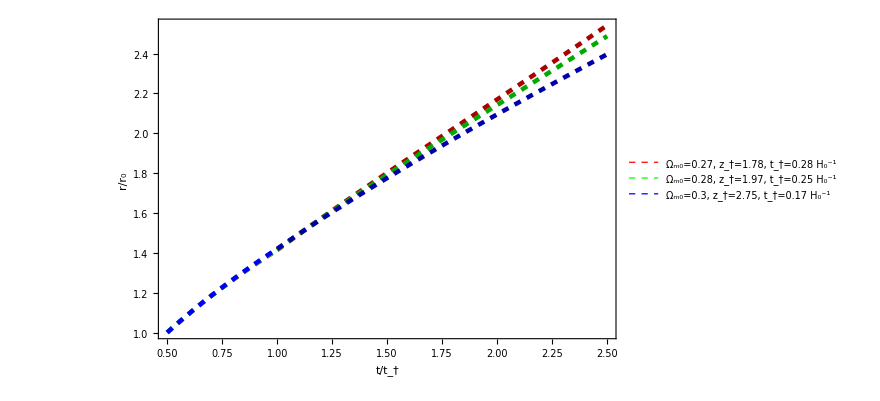

```mathematica
Plot[{cutoff1[τ,1] rminus[τ,0.2738,0.28086317827196966,A[0.2738,0.28086317827196966],B[0.2738,0.28086317827196966]],cutoff1[τ,1] rminus[τ,0.282,0.2455709849832619,A[0.282,0.2455709849832619],B[0.282,0.2455709849832619]],cutoff1[τ,1] rminus[τ,0.2983,0.16936284198307755,A[0.2983,0.16936284198307755],B[0.2983,0.16936284198307755]],cutoff[τ,1] rplus[τ,0.2738,0.28086317827196966,H[0.2738,0.28086317827196966,A[0.2738,0.28086317827196966],B[0.2738,0.28086317827196966]],F[0.2738,0.28086317827196966,A[0.2738,0.28086317827196966],B[0.2738,0.28086317827196966]]],cutoff[τ,1] rplus[τ,0.282,0.2455709849832619,H[0.282,0.2455709849832619,A[0.282,0.2455709849832619],B[0.282,0.2455709849832619]],F[0.282,0.2455709849832619,A[0.282,0.2455709849832619],B[0.282,0.2455709849832619]]],cutoff[τ,1] rplus[τ,0.2983,0.16936284198307755,H[0.2983,0.16936284198307755,A[0.2983,0.16936284198307755],B[0.2983,0.16936284198307755]],F[0.2983,0.16936284198307755,A[0.2983,0.16936284198307755],B[0.2983,0.16936284198307755]]]},{τ,0.5,2.5},FrameLabel->{{Style["r/\!\(\*SubscriptBox[\(r\), \(0\)]\)",FontSize->20],None},{Style["t/\!\(\*SubscriptBox[\(t\), \(†\)]\)",FontSize->20],None}},PlotLegends->Placed[LineLegend[{"\!\(\*SubscriptBox[\(Ω\), \(m0\)]\)=0.27, z_†=1.78, t_†=0.28 H_0^-1","\!\(\*SubscriptBox[\(Ω\), \(m0\)]\)=0.28, z_†=1.97, t_†=0.25 H_0^-1","\!\(\*SubscriptBox[\(Ω\), \(m0\)]\)=0.3, z_†=2.75, t_†=0.17 H_0^-1"},LabelStyle->{FontSize->20}],{Right,Bottom}],PlotStyle->{{Red,Dashed,Thickness[0.005]},{Green,Dashed,Thickness[0.005]},{Blue,Dashed,Thickness[0.005]},{Darker[Red],Dashed,Thickness[0.005]},{Darker[Green],Dashed,Thickness[0.005]},{Darker[Blue],Dashed,Thickness[0.005]}},LabelStyle->{FontSize->20},Frame->True]
```